# Systematic Randomness Testing

Emmy/Noah Blumenthal

Jonathan Gorard

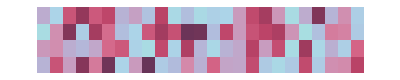

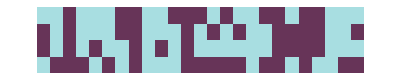

## Introduction

## Chi square equidistribution test

The first test we will examine is a relatively simple, ubiquitous test: the chi square test for independence. In this approach we will use the chi square test to measure how the observed values differ from expected values.

#### Zeros and ones

The expected value distribution of zeros and ones is very simple. There is a 1/2 probability that a variate will be 0 and a 1/2 probability that a variate will be 1. Therefore, we can set up a statistic like the following:

```mathematica
chiSquareTestStatIntegers[seq_]:=(Total[seq]-1/2 Length[seq])^2/(1/2 Length[seq])(*observed number of ones*)+((Length[seq]-Total[seq])-1/2 Length[seq])^2/(1/2 Length[seq])(*observed number of zeros*);
```

We know that this statistic will follow a chi square distribution with ν = 1. Let’s confirm:

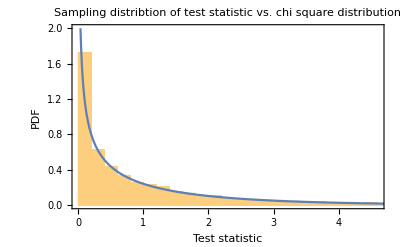

```mathematica
Show[Histogram[Table[chiSquareTestStatIntegers[RandomInteger[{0,1},10000]],100000],Automatic,"PDF"],Plot[PDF[ChiSquareDistribution[1],x],{x,0,10},PlotRange->{0,2}],]
```

Therefore, we can construct a p-value as follows:

```mathematica
chiSquareTestPValueIntegers[seq_]:=1.-CDF[ChiSquareDistribution[1],chiSquareTestStatIntegers[seq]]
```

To check our work, we can construct a probability plot comparing the distribution of p-values to the uniform distribution.

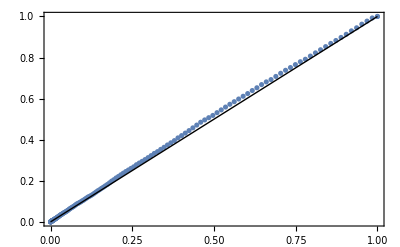

```mathematica
ProbabilityPlot[Table[chiSquareTestPValueIntegers[RandomInteger[{0,1},10000]],10000],UniformDistribution[]]
```

We observe that the rate of type-I error behaves as expected for a well-functioning test. This, of course, assumes that the pseudo–random number generator that is RandomInteger is truly “random”—whatever that may mean.

#### Random reals between zero and one

Again, with the chi square test for independence, we must compare observed values to expected values. For continuous distributions, we must choose bins in which we have expected values. For our purposes, we will choose bins of size 1/n where n is the length of the sequence. Using this bin specification, we know that the expected number of numbers we should observe in each bin should be 1. With this information, we can create a test statistic:

```mathematica
chiSquareTestStatReals[seq_]:=Total[(BinCounts[seq,1/Length[seq]]-1)^2/1](*note we use the listable atribute of squaring and basic arithmetic*)
```

This distribution should follow the chi square distribution with ν = n -2 where n is the length of the sequence. Let’s confirm:

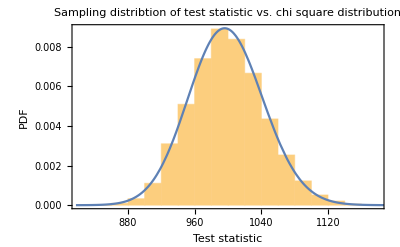

```mathematica
Show[Histogram[Table[chiSquareTestStatReals[RandomReal[{0,1},1000]],10000],Automatic,"PDF"],Plot[PDF[ChiSquareDistribution[998],x],{x,0,1500},],]
```

We can then construct a p-value:

```mathematica
chiSquareTestPValueReals[seq_]:=1.-CDF[ChiSquareDistribution[Length[seq]-2],chiSquareTestStatReals[seq]];
```

Again, to check our work, we can construct a probability plot comparing the distribution of p-values to the uniform distribution.

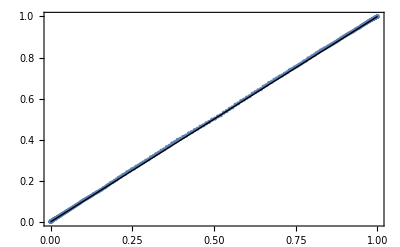

```mathematica
ProbabilityPlot[Table[chiSquareTestPValueReals[RandomReal[{0,1},1000]],10000],UniformDistribution[]]
```

Again, it seems as if we are successful!

## The Kolmogorov–Smirnov distribution fit test

The Kolmogorov–Smirnov test is a power distribution fit test that compares an empirical CDF to a known CDF. The Kolmogorov–Smirnov test is relatively simple to formulate, but fortunately, it is already implemented in the Wolfram Language. We can then apply it to test for equidistribution of a sequence:

```mathematica
sequence=RandomReal[{0,1},10000];
```

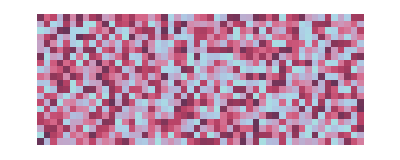

```mathematica
ArrayPlot[Partition[Take[sequence,1000],50],ImageSize->Full,ColorFunction->"CandyColors"]
```

```mathematica
KolmogorovSmirnovTest[sequence,UniformDistribution[]]
```

0.383461

It is important to note that the Kolmogorov–Smirnov test does not handle ties very well:

```mathematica
duplicateSequence=Flatten[{sequence,sequence}];
```

```mathematica
KolmogorovSmirnovTest[duplicateSequence,UniformDistribution[]]
```

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

0.0745876

#### A final note on equidistribution tests

Equidistribution tests are very easily fooled! They do not care about order, permutations, runs, spectra, or anything like these complex properties. Here’s an example of how equidistribution tests is completely fooled:

```mathematica
nonrandomSequence=Range[0,1,.0001];
```

```mathematica
KolmogorovSmirnovTest[nonrandomSequence,UniformDistribution[]]
```

1.

```mathematica
chiSquareTestPValueReals[nonrandomSequence]
```

General::munfl: Exp[-37587.9] is too small to represent as a normalized machine number; precision may be lost.

1.

## Serial test

## Runs tests

### How long are runs in a sequence?

### How many runs do we expect a sequence to have?

## Differences tests

## Overlapping permutations

## Spectral tests

## Discussion